```mathematica
SetDirectory["Z:\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\03\\06"]
```

Z:\NLab\ASTeC\Projects\VELA\Work\2018\03\06

```mathematica
data=Import["Charge_vs_Position_Phase.xlsx"][[2]]
```

{{,,,,,Reticule Marks:,2Down,1.5left,},{,Relative Position,,,,,,,RF PHASE = 160},{,x,y,WCM Raw pWb,WCM Signal mV,laser uJ,,,},{,0.,0.,116.,0.748,4.27,,,},{,-1.,-1.,274.,1.718,4.18,,,},{,-0.5,-1.,237.,1.55,4.18,,,},{,0.,-1.,237.,1.56,4.2,,,},{,0.5,-1.,249.,1.61,4.19,,,},{,1.,-1.,259.,1.62,4.15,,,},{,-1.,-0.5,234.,1.56,4.13,,,},{,-0.5,-0.5,196.,1.32,4.13,,,},{,0.,-0.5,184.,1.22,4.18,,,},{,0.5,-0.5,195.,1.28,4.16,,,},{,1.,-0.5,206.,1.37,4.16,,,},{,-1.,0.,210.,1.3,4.16,,,},{,-0.5,0.,163.,1.01,4.15,,,},{,0.,0.,129.,0.781,4.15,,,},{,0.5,0.,160.,0.995,4.14,,,},{,1.,0.,196.,1.2,4.19,,,},{,-1.,0.5,188.,1.16,4.19,,,},{,-0.5,0.5,151.,0.931,4.18,,,},{,0.,0.5,136.,0.85,4.16,,,},{,0.5,0.5,166.,1.,4.19,,,},{,1.,0.5,192.,1.18,4.2,,,},{,-1.,1.,197.,1.18,4.19,,,},{,-0.5,1.,157.,0.96,4.17,,,},{,0.,1.,151.,0.93,4.19,,,},{,0.5,1.,166.,1.04,4.19,,,},{,1.,1.,193.,1.19,4.2,,,}}

```mathematica
ListPlot3D[Drop[data,3][[All,{2,3,5}]],ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Clear[x,y,z]
```

```mathematica
Log[10,0]
```

-∞

```mathematica
StringReplace[ToString[RotationMatrix[theta,{0,1,0}]],{"{"->"[","}"->"]","Sin[theta]"->"np.sin(theta)","Cos[theta]"->"np.cos(theta)","-"->"-1*"}]
```

[[np.cos(theta), 0, np.sin(theta)], [0, 1, 0], [-1*np.sin(theta), 0, np.cos(theta)]]

```mathematica
globaloffset={-0.149171,0,6.187};
```

```mathematica
pos={{0,0,5.82687},globaloffset,{-0.384336,0,6.42217},{-0.589397,0,6.62723},{-0.794458,0,6.83229},{-0.944068,0,6.9819}};
```

```mathematica
(RotationMatrix[45Degree,{0,1,0}].(#-globaloffset))&/@pos
```

{{-0.149171,0.,-0.36013},{0.,0.,0.},{3.53553×10^-6,0.,0.332577},{2.82843×10^-6,0.,0.622576},{2.12132×10^-6,0.,0.912576},{2.12132×10^-6,0.,1.12416}}

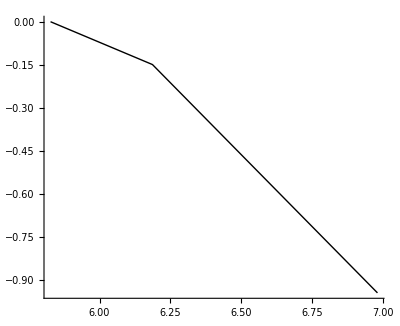

```mathematica
Graphics[Line[#[[{3,1}]]&/@pos],Axes->True]
```

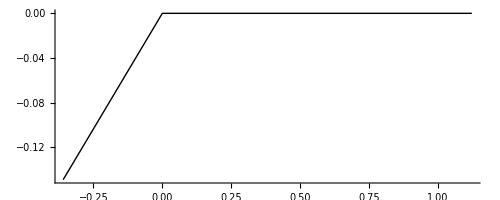

```mathematica
Graphics[Line[(RotationMatrix[45Degree,{0,1,0}].#-RotationMatrix[45Degree,{0,1,0}].globaloffset)[[{3,1}]]&/@pos],Axes->True]
```

```mathematica
Graphics[Line[(RotationMatrix[45Degree,{0,1,0}].(#-globaloffset))[[{3,1}]]&/@pos],Axes->True]
```

-Graphics-

```mathematica
pts={{-0.2057394566101931,0,-0.30356125762340347},{-0.08000069821724301,0,-9.716488191119366*^-07},{0.08000050178275656,0,-9.71648819542148*^-07},{-0.09260150460575994,0,-0.4166991726549374}}
```

{{-0.205739,0,-0.303561},{-0.0800007,0,-9.71649×10^-7},{0.0800005,0,-9.71649×10^-7},{-0.0926015,0,-0.416699}}

```mathematica
pts[[{1,4,3,2},{1,3}]]
```

{{-0.205739,-0.303561},{-0.0926015,-0.416699},{0.0800005,-9.71649×10^-7},{-0.0800007,-9.71649×10^-7}}

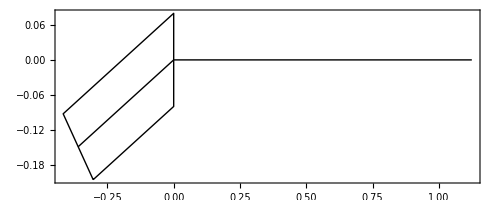

```mathematica
Show[Graphics[Line[pts[[{1,2,3,4,1},{3,1}]]],Frame->True],
Graphics[Line[(RotationMatrix[45Degree,{0,1,0}].(#-globaloffset))[[{3,1}]]&/@pos],Axes->True,AspectRatio->1]
]
```

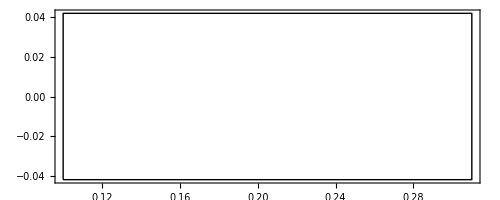

```mathematica
pts=ToExpression[StringReplace["[[-0.041999309241934846, 0, 0.10005490243122921], [-0.041999309241934568, 0, 0.31005490243122946], [0.042000690758065173, 0, 0.31005490243122924], [0.042000690758064882, 0, 0.10005490243122897]]",{"array(["->"{","])"->"}","["->"{","]"->"}"}]];
Graphics[Line[pts[[{1,2,3,4,1},{3,1}]]],Frame->True]
```

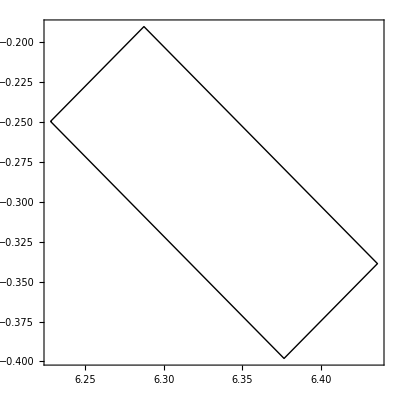

```mathematica
pts=ToExpression[StringReplace["[array([-0.24961849,0.,6.22805152]),array([-0.39811089,0.,6.37654397]),array([-0.33871391,0.,6.43594093]),array([-0.19022151,0.,6.28744848])]",{"array(["->"{","])"->"}","["->"{","]"->"}"}]];
Graphics[Line[pts[[{1,2,3,4,1},{3,1}]]],Frame->True]
```

```mathematica
drawPythonDipole[str_String]:=Block[{},
pts=ToExpression[StringReplace[str,{"array(["->"{","])"->"}","["->"{","]"->"}","e-"->"*^-","e+"->"*^","e"->"*^"}]];
Print[Line[#[[{1,2,3,4,1},{3,1}]]]&/@Partition[pts,4]];
Graphics[Line[#[[{1,2,3,4,1},{3,1}]]]&/@Partition[pts,4],Frame->True]
]
```

{Line[{{26.0651,-0.0401962},{26.2657,-0.0301555},{26.2657,0.0502369},{26.0651,0.0401962},{26.0651,-0.0401962}}],Line[{{27.7583,0.119595},{27.9589,0.129635},{27.9589,0.210028},{27.7583,0.199987},{27.7583,0.119595}}],Line[{{29.2589,0.129635},{29.4595,0.119595},{29.4595,0.199987},{29.2589,0.210028},{29.2589,0.129635}}],Line[{{30.9521,-0.0301555},{31.1527,-0.0401962},{31.1527,0.0401962},{30.9521,0.0502369},{30.9521,-0.0301555}}]}

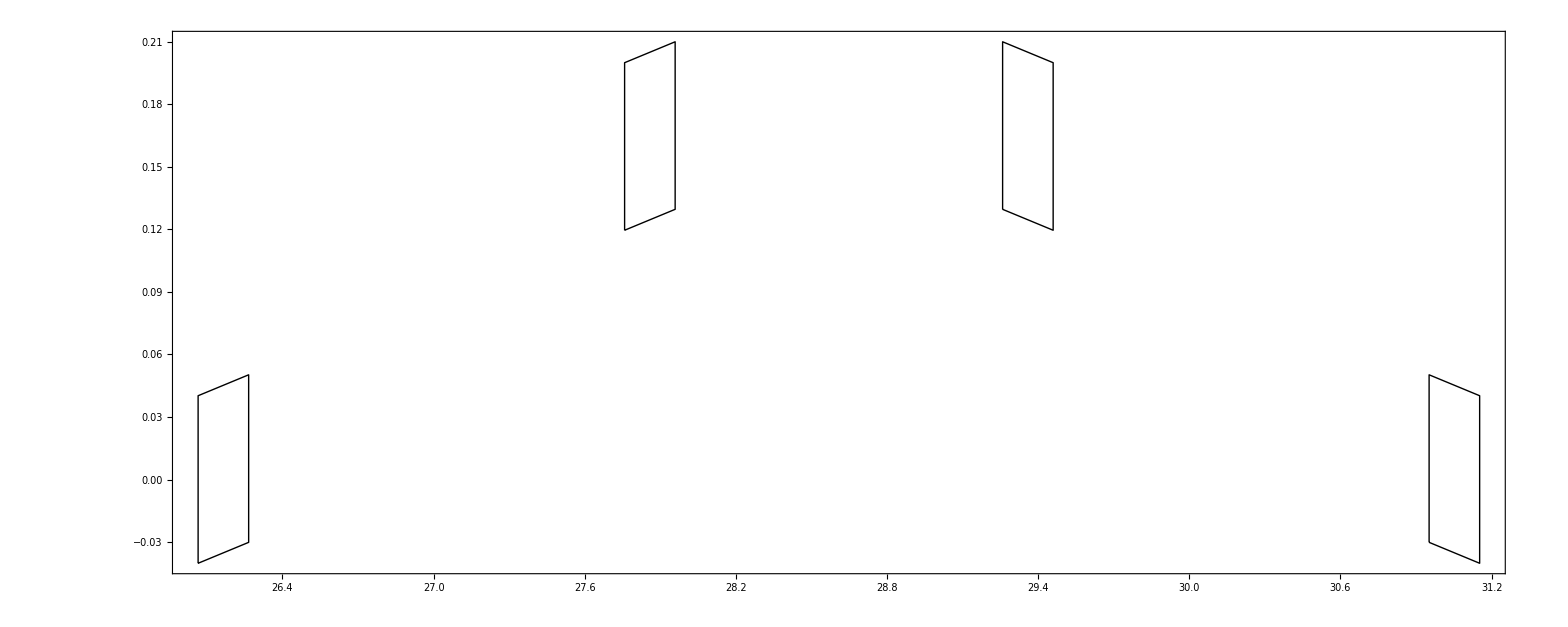

```mathematica
drawPythonDipole["[array([ -0.0401962,   0.       ,  26.0651   ]), array([ -0.03015552,   0.        ,  26.2657462 ]), array([  0.05023688,   0.        ,  26.2657462 ]), array([  0.0401962,   0.
  ,  26.0651   ]), array([  0.1195946 ,   0.        ,  27.75825245]), array([  0.12963528,   0.        ,  27.95889865]), array([  0.21002768,   0.        ,  27.95889865]), array([  0.199987  ,   0.        ,  27.75825245]), array([  0.12963528,   0.        ,  29.25889865]), array([  0.1195946 ,   0.        ,  29.45954485]), array([  0.199987  ,   0.        ,  29.45954485]), array([  0.21002768,   0.        ,  29.25889865]), array([ -3.01555263e-02,   0.00000000e+00,   3.09520511e+01]), array([ -0.04019621,   0.        ,  31.15269729]), array([  0.04019619,   0.        ,  31.15269729]), array([  0.05023687,   0.        ,  30.95205109])]"]
```

## Gun Fields

```mathematica
gun=Import["C:\\anaconda32\\Work\\OnlineModel\\MasterLattice\\Data_Files\\HRRG_1D_RF.dat"];
```

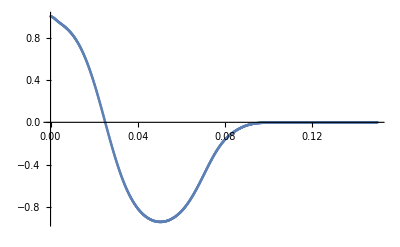

```mathematica
ListPlot[gun]
```

```mathematica
Max[gun[[All,1]]]
```

0.15

```mathematica
gun=Import["C:\\anaconda32\\Work\\OnlineModel\\MasterLattice\\Data_Files\\bas_gun.txt","Table"];
```

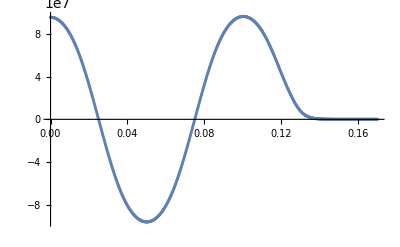

```mathematica
ListPlot[gun]
```

```mathematica
lsol=Import["C:\\anaconda32\\Work\\OnlineModel\\MasterLattice\\Data_Files\\SwissFEL_linac_sols.dat","Table"];
```

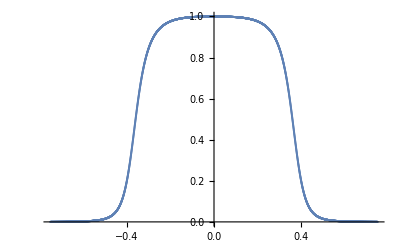

```mathematica
ListPlot[lsol]
```

```mathematica
Max[gun[[All,1]]]
```

0.17

```mathematica
UnitConvert[Quantity[250,"pC"]/512/Quantity["e"]]//N
```

3.04761×10^6

```mathematica
45Degree//N
```

0.785398

```mathematica
1/360*2*Pi//N
```

0.0174533

```mathematica
26250*1.2
```

31500.

```mathematica
31500*1.2
```

37800.

```mathematica
RotationMatrix[-45Degree,{0,1,0}]//N
```

{{0.707107,0.,-0.707107},{0.,1.,0.},{0.707107,0.,0.707107}}

```mathematica
{1.49171701*^-01, 1.84856202*^-07,-4.66797980*^-01}.RotationMatrix[-45Degree,{0,1,0}]
```

{-0.224596,1.84856×10^-7,-0.435556}

```mathematica
Directory[]
```

\\apclara1\jkj62\Online-Model\ASTRAFramework\ASTRAGeneral\test_longitudinal

## Testing rotations

```mathematica
<<astrainterpret`
```

```mathematica
Import[beam]
```

{/Parameters/Rotation,/Parameters/Source,/Parameters/Starting_Position,/Parameters/centered,/Parameters/code,/Parameters/npart,/Parameters/particle_mass,/Parameters/total_charge,/beam/beam,/beam/columns,/beam/reference_particle,/beam/units}

```mathematica
readHDF5Beam[filename_,opts___Rule]:=Block[{unrotate,verbose,cols,startposition,rotation},
unrotate=Global`HDF5Normalise/.{opts}/.{Global`HDF5Normalise->True};
verbose=Global`HDF5Verbose/.{opts}/.{Global`HDF5Verbose->False};
cols=Import[beam,"/beam/columns"];
Clear[Evaluate[#]]&/@cols;
beamdata=Transpose[Import[beam,"/beam/beam"]];
startposition=Import[beam,"/Parameters/Starting_Position"];
rotation=Import[beam,"/Parameters/Rotation"];
If[unrotate,
beamdata[[{1,2,3}]]=Transpose[(#-startposition&/@Transpose[beamdata[[{1,2,3}]]]).RotationMatrix[rotation,{0,1,0}]];
beamdata[[{4,5,6}]]=Transpose[((#&/@Transpose[beamdata[[{4,5,6}]]]).RotationMatrix[rotation,{0,1,0}])];
];
MapThread[(Evaluate[Symbol@#1]=#2)&,{cols,beamdata}];
params=Import[beam,"/Parameters"];
Clear[Evaluate[StringReplace[#1,{"_"->"£","-"->"$"}]]]&/@Keys[params];
MapThread[(Evaluate[Symbol@StringReplace[#1,{"_"->"£","-"->"$"}]]=#2)&,{Keys[params],Values[params]}];
If[verbose,
Print["Parameter(s) Assigned: ",Keys[params]];
Print["Variables(s) Assigned: ",cols];
];
]
```

```mathematica
readHDF5Beam[beam="C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\CLA-S05-MARK-01.hdf5",HDF5Verbose->True]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

```mathematica
{x,y,z,cpx,cpy,cpz}[[All,1]]
```

{-4.67025×10^-6,-0.0000160477,0.0000514678,189.523,-334.654,1.55683×10^8}

```mathematica
Import[beam,"/beam/reference_particle"]
```

{-4.67025×10^-6,-0.0000160477,25.8252,189.523,-334.654,1.55683×10^8,86.1439,-0.000488281,1.,5.}

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\S05.2583.001",ASTRAVerbose->True]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

```mathematica
{x,y,z,px,py,pz}[[All,1]]
```

{-4.67025×10^-6,-0.0000160477,25.8252,189.523,-334.654,1.55683×10^8}

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\CLA-S05-MARK-01.astra",ASTRAVerbose->True]
```

Clear::wrsym: Symbol charge is Protected.

Set::wrsym: Symbol charge is Protected.

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

```mathematica
clock
```

{86.1439,0.000813538,-0.000787618,0.00130605,-0.00194933,0.00235416,-0.00256908,0.0018557,-0.000729162,-0.00165822,-0.00175485,0.00172077,0.00226476,0.000459729,-0.00166271,7.19064×10^-6,-0.000154627,0.00229456,0.00145265,-0.00101157,-0.00023003,-0.000763461,0.00083069,-0.00279953,0.00101046,-0.00188126,-0.000354919,-0.00172779,-0.000251913,-0.00137492,-0.000405483,-0.00159874,-0.00105266,-0.00162729,0.000361075,0.00219965,-0.000535721,-0.00292869,-0.0025772,-0.00129113,0.00245609,0.00024472,-0.000537514,-0.000510766,0.00111047,-0.00243485,-0.00175858,0.000513869,-0.00107135,-0.000864731,0.000513373,0.000336137,-0.00203723,-0.00229994,0.001754,0.000636801,0.000394957,-0.00214839,0.00160694,-0.000158126,0.00276685,0.000517687,0.00160369,-0.000988337,0.00131418,0.000564174,0.00274754,0.00256628,0.00134667,0.000106739,-0.00245979,0.00252028,0.00210249,0.000107879,-0.00301855,0.0000852061,0.000676496,0.00129294,0.00216286,0.00144462,-0.0022617,0.000719191,-0.00148881,0.0000897178,0.000526779,0.00219526,-0.000473715,-0.000237305,0.00134345,0.00213245,-0.000200534,-0.00191932,-0.00131172,0.000388447,-0.00222934,-0.00198184,0.00123358,-0.00180369,0.000607438,0.00142481,0.00240157,0.00221475,-0.00044677,-0.000417376,-0.000529558,-0.000216591,0.00100048,-0.00123174,0.00174276,-0.000461598,0.000480607,0.000683381,-0.002506,0.000945406,0.00123966,0.00245431,0.00166604,-0.0015215,-3.76583×10^-6,-0.000138584,0.00106752,0.000604137,-0.00181115,0.000272959,-0.000451543,-0.00177342,-0.000487271,-0.0000600956,-0.00295685,-0.00088253,-0.00114849,-0.00123311,-0.00106176,-0.000580587,-0.00053718,-0.000176015,-0.00187688,-0.00123603,-0.00189433,-0.00323203,0.00261429,0.000859561,-0.0020996,-0.00273723,0.000266672,0.00176843,-0.000175601,-0.000196069,-0.00170471,-0.00289336,-0.00210816,-0.0000833038,-0.000223881,-0.00128812,-0.0016727,-0.000379983,-0.00132466,-0.00267619,0.00118081,-0.00092092,0.00172044,-0.00235139,0.00262086,0.00230092,-0.00307544,0.00097484,0.00272118,0.000509423,-0.00215367,0.0016207,0.00219059,-0.0010571,-0.00226441,-0.00273067,-0.000710282,-0.00116561,0.00242697,0.00246134,0.00208108,-0.000997953,0.00216733,-0.000394486,-0.0012926,-0.00328536,0.000692943,-0.000177044,-0.00242093,-0.00307886,-0.00300365,0.00216313,-0.00182357,0.0000932435,-0.00181036,-0.00239918,-0.00232148,0.000653957,-0.00172668,0.00258024,-0.0000882222,-0.000295944,0.000961907,0.00119315,0.00286548,-0.000923342,0.00180264,-0.00228492,0.000568094,-0.00103907,-0.00262979,-0.00268822,0.00148394,-0.00121181,-0.000220698,-0.0018411,-0.000689241,-0.00085355,0.000597457,-0.00228883,0.00174419,-0.00191019,0.0000841457,-0.00238534,0.000865009,-0.00275968,0.00205511,0.00042008,0.0017829,-0.000292209,-0.000459638,-0.00165231,-0.00115046,0.000797806,0.000532763,-0.00240284,0.000354091,-0.0025024,0.000116069,0.00173832,-0.000603566,-0.0027747,-0.000961716,-0.00321436,-0.000274066,-0.00207763,0.000555973,-0.00222002,-0.00209413,-0.00228321,-0.000748689,0.00147367,0.00209791,0.0014963,-0.0021752,-0.00156219,0.00248859,-0.00049788,0.00141993,0.00253028,0.00221499,-1.64212×10^-6,0.000389724,-0.00210024,0.00109889,0.000607348,0.000889543,-0.00334448,-0.00180269,-0.000917736,0.00174322,0.000899932,-0.000394534,-0.000544554,0.00176183,0.000318006,0.00270458,0.00113989,0.00187224,0.000228564,0.00041378,-0.0000147435,0.00189053,0.000988247,-0.001552,-0.001903,0.000135383,0.00261912,-0.000105131,0.00116571,-0.00136808,-0.00200823,0.00189252,-0.000415909,-0.00146654,0.00156963,0.00121336,0.00205169,0.00186704,-0.000374627,-0.00108985,0.00229647,-0.00173351,-0.00128505,-0.00122878,0.00102303,-0.00201176,-0.000597577,0.001248,0.000840118,0.0020002,-0.000562729,-0.00141286,-0.000351974,0.0026534,0.00221315,0.00185531,-0.00255344,-0.00105243,0.000460036,0.00213927,0.0000154979,-0.00175838,0.00167638,0.00267075,0.000817404,-0.00175786,0.0000248,-0.00120486,-0.00281349,0.000390369,-0.00213174,-0.00173578,0.000794949,0.00134487,-0.00245727,0.000921701,-0.000204153,0.00162712,-0.00277845,-0.00265566,-0.000306824,-0.00268556,0.000650143,-0.0024995,0.00188882,0.00234428,-0.000566952,-0.000463094,0.00222981,-0.000854787,-0.00235292,0.00212198,-0.00289576,-0.000315834,-0.000284758,-0.00063544,0.00128103,0.00190198,0.00133502,0.0000436628,0.00201295,0.00237639,0.0000118881,0.000248011,-0.00100882,0.00171335,0.00242209,0.00247053,-0.00184615,-0.000058137,-0.000280043,-0.00188453,0.00100829,-0.00233374,0.00157897,-0.000522723,-0.00279926,-0.00172393,-0.000749456,0.00153336,-0.0029108,0.00131247,0.000968574,0.000805665,-0.0031315,-0.000527051,0.000242066,-0.0000507095,-0.00151175,-0.00297732,0.00116538,-0.0024078,-0.000795458,0.000327371,0.000641237,-0.00111689,0.00072133,0.00238595,-0.000821856,-0.000382085,0.00070208,6.66691×10^-6,-0.00080732,-0.00301344,0.00157423,0.000590911,0.000667425,-0.000876179,0.00214732,-0.00196501,0.0022553,0.000621123,0.000607814,0.00156305,-0.00114907,0.000106081,0.000511705,0.0014136,-0.00142351,0.00139454,0.00263666,0.00165866,0.00127767,0.000118693,-0.00134828,-0.000961861,0.000443822,0.000793301,0.0000309043,-0.000773452,-0.00110078,-0.00128064,-0.00214174,0.000994086,0.00181461,0.000412039,0.00116642,-0.000893369,0.00143041,0.00212904,-0.00150777,0.000038487,-0.00107841,-0.000890799,0.0006983,-0.00134044,0.000373697,0.000459086,-0.00248757,-0.000666094,-0.00173483,-0.00179511,-0.0022433,0.00158262,0.00141107,-0.00158376,-0.000991138,0.00225582,-0.00246034,0.0011265,-0.00254809,0.000418226,0.00141264,0.0000880981,-0.00101255,-0.000680855,-0.000919322,0.000950338,-0.00259465,0.0000360033,-0.00185107,0.00118881,0.00128881,0.000157932,-0.00305235,0.000535053,-0.000391825,-0.000500617,-0.000279604,-0.0016858,-0.00140972,-0.00199279,-0.00267567,-0.00131349,-0.000254775,0.00152786,0.000952796,0.000571354,-0.0013471,0.000556824,-0.00198679,0.00274886,-0.000976215,-0.00154603,-0.00130576,0.00107077,-0.0024945,0.00115902,-0.00243216,-0.00218016,-0.00180172,0.00132016,0.0000971674,-0.000852653,-0.000460895,-0.000909829,0.00226963,-0.0019435,-0.00160568,0.0000159178,0.000194102,-0.000589697,0.000114055}

#### CLA-S01-DIA-BPM-01.hdf5

```mathematica
beam="C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\EBT-INJ-PSS-SHUT-02.hdf5";
```

```mathematica
readHDF5Beam[beam,HDF5Normalise->True]
```

```mathematica
Max[x]-Min[x]
```

0.00573288

```mathematica
Max[pz]
Min[pz]
```

3.55207×10^7

3.48932×10^7

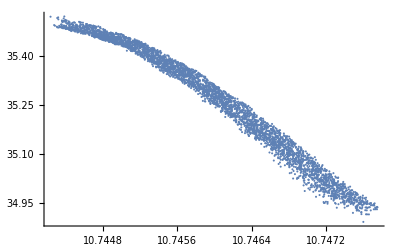

```mathematica
ListPlot[Transpose[{z,10^-6*cpz}],PlotRange->All]
```

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\vela.1126.001"]
```

```mathematica
Max[pz]
Min[pz]
```

3.55207×10^7

3.48932×10^7

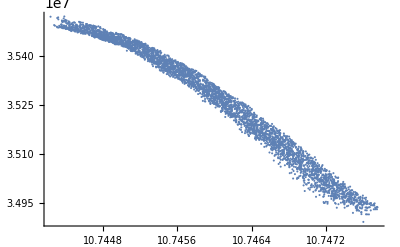

```mathematica
ListPlot[Transpose[{z,pz}],PlotRange->All]
```

#### End of Injector

```mathematica
beam="C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\CLA-S02-APER-01.hdf5";
```

```mathematica
readHDF5Beam[beam,HDF5Normalise->False]
```

```mathematica
Max[x]-Min[x]
```

0.00184102

```mathematica
Max[pz]
Min[pz]
```

7.08185×10^7

3.52978×10^7

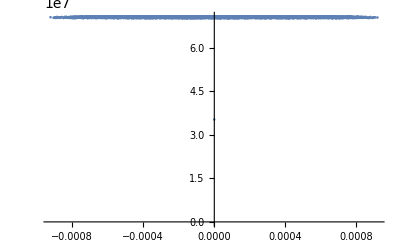

```mathematica
ListPlot[Transpose[{x,pz}],PlotRange->All]
```

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\injector400.0337.001"]
```

```mathematica
Max[x]-Min[x]
```

0.00184102

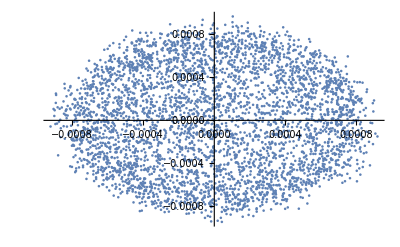

```mathematica
ListPlot[Transpose[{x,y}],PlotRange->All]
```

#### End of S02

```mathematica
beam="C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\CLA-C2V-MARK-01.hdf5";
```

```mathematica
readHDF5Beam[beam]
```

```mathematica
Max[x]-Min[x]
```

0.00181227

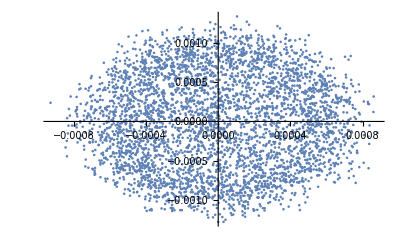

```mathematica
ListPlot[Transpose[{x,y}],PlotRange->All]
```

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\s02.0236.001"]
```

```mathematica
Max[x]-Min[x]
```

0.00181227

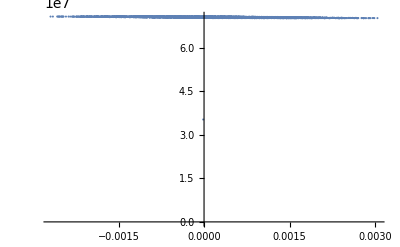

```mathematica
ListPlot[Transpose[{x,pz}],PlotRange->All]
```

#### End of C2V

```mathematica
beam="C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\CLA-C2V-DIA-SCR-01-W.hdf5";
```

```mathematica
readHDF5Beam[beam,HDF5Verbose->True,HDF5Normalise->True]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

```mathematica
Max[x]-Min[x]
```

0.00572617

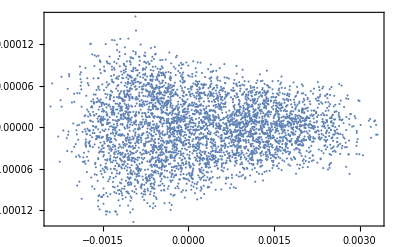

```mathematica
ListPlot[Transpose[{x,y}],PlotRange->All,Frame->True]
```

```mathematica
Clear[x,y,z,px,py,pz]
```

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\c2v.0155.001",ASTRAVerbose->True]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

```mathematica
Max[x]-Min[x]
```

0.00572617

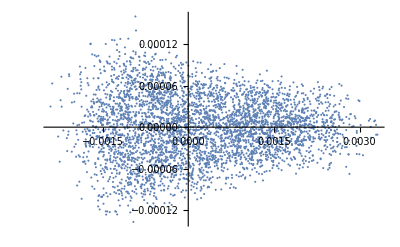

```mathematica
ListPlot[Transpose[{x,y}],PlotRange->All]
```

```mathematica
startpos=Mean[Import[beam,"/beam/beam"]][[1;;3]]
```

{-0.943907,-2.12512×10^-7,6.98206}

```mathematica
Import[beam,"/beam/reference_particle"]
```

{-0.944033,-9.96771×10^-8,6.98181,-2.49573×10^7,-43.4566,2.49616×10^7,13.2753,-0.0000610352,1.,5.}

```mathematica
startposition=Import[beam,"/Parameters/Starting_Position"]
```

{-0.944068,0.,6.9819}

```mathematica
beamdata=Import[beam,"/beam/beam"];
```

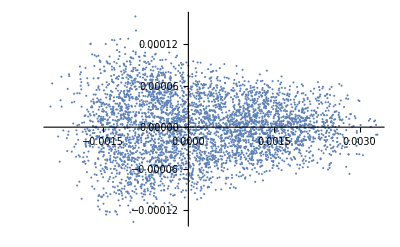

```mathematica
ListPlot[((#-startposition&/@beamdata[[All,{1,2,3}]]).RotationMatrix[Import[beam,"/Parameters/Rotation"],{0,1,0}])[[All,{1,2}]]]
```

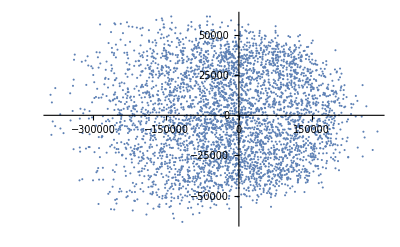

```mathematica
ListPlot[((#&/@beamdata[[All,{4,5,6}]]).RotationMatrix[Import[beam,"/Parameters/Rotation"],{0,1,0}])[[All,{1,2}]]]
```

```mathematica
offset={-1.25,0,7.49879};
```

```mathematica
(startpos-offset).RotationMatrix[90Degree,{0,1,0}]
```

{0.516729,-2.12512×10^-7,0.306093}

```mathematica
Quiet[ASTRABeamInterpret[StringReplace[beam,{".hdf5"->".astra"}]]]
{x,y,z,px,py,pz}[[All,1]]
```

{0.305967,-9.96771×10^-8,-0.51698,-2.49573×10^7,-43.4566,2.49616×10^7}

#### End of VELA

```mathematica
beam="C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\EBT-INJ-PSS-SHUT-02.hdf5";
```

```mathematica
readHDF5Beam[beam,HDF5Verbose->True,HDF5Normalise->True]
```

Parameter(s) Assigned: {Rotation,Source,Starting_Position,centered,code,npart,particle_mass,total_charge}

Variables(s) Assigned: {x,y,z,cpx,cpy,cpz,t,q}

```mathematica
Max[x]-Min[x]
```

0.00573288

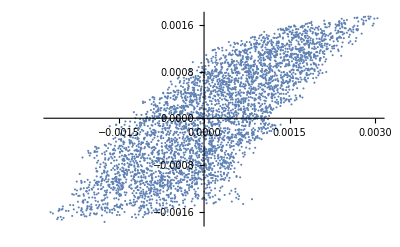

```mathematica
ListPlot[Transpose[{x,z}],PlotRange->All]
```

```mathematica
Clear[x,y,z,px,py,pz]
```

```mathematica
ASTRABeamInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\vela.1126.001",ASTRAVerbose->True]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

```mathematica
Max[pz]
Min[pz]
```

7.08185×10^7

3.52978×10^7

```mathematica
ListPlot[Transpose[{x,pz}],PlotRange->All]
```

-Graphics-

```mathematica
startpos=Mean[Import[beam,"/beam/beam"]][[1;;3]]
```

{-1.24986,0.0000126049,18.2448}

```mathematica
Import[beam,"/beam/reference_particle"]
```

{-1.25001,1.09826×10^-6,18.2447,1063.07,24.705,3.52978×10^7,41.6723,-0.0000610352,1.,5.}

```mathematica
Import[beam]
```

{/Parameters/Rotation,/Parameters/Source,/Parameters/Starting_Position,/Parameters/centered,/Parameters/code,/Parameters/npart,/Parameters/particle_mass,/Parameters/total_charge,/beam/beam,/beam/columns,/beam/reference_particle,/beam/units}

```mathematica
Import[beam,"/Parameters/Starting_Position"]
```

{-1.25,0.,18.2448}

```mathematica
Import[beam,"/Parameters/Rotation"]
```

0.

```mathematica
offset={-1.25,0,7.49879};
```

```mathematica
(startpos-offset).RotationMatrix[90Degree,{0,1,0}]
```

{-10.746,0.0000126049,0.00014029}

```mathematica
Quiet[ASTRABeamInterpret[StringReplace[beam,{".hdf5"->".astra"}]]]
{x,y,z,px,py,pz}[[All,1]]
```

{-0.0000147406,1.09826×10^-6,10.7459,1063.07,24.705,3.52978×10^7}

## Testing emit files

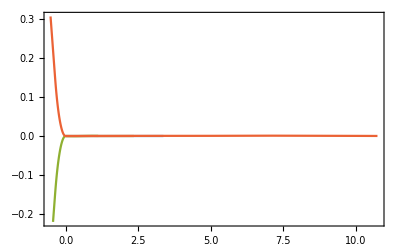

```mathematica
lastZ=0;
ListLinePlot[Block[{},
ASTRAemitInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\"<>#];lastZ=z[[-1]];
Transpose[{z,10^-3 xavr}]]&/@{"injector400.Xemit.001","s02.Xemit.001","c2v.Xemit.001","vela.Xemit.001"},PlotRange->All,Frame->True]
```

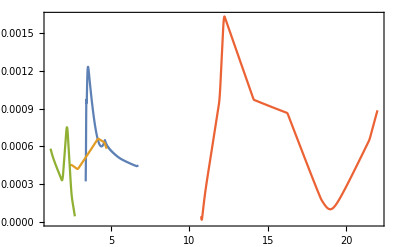

```mathematica
lastZ=0;
ListLinePlot[Block[{},
ASTRAemitInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\C2V\\"<>#];lastZ=z[[-1]];
Transpose[{lastZ+z-z[[1]],10^-3 yrms}]]&/@{"injector400.Xemit.001","s02.Xemit.001","c2v.Xemit.001","vela.Xemit.001"},PlotRange->All,Frame->True]
```

## Testing Elegant

```mathematica
<<sddsInterpret`
```

```mathematica
0.076607+0.02872
```

0.105327

```mathematica
3.4768-3.37147
```

0.10533

```mathematica
ASTRAemitInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\"<>#<>".Zemit.001"&/@{"S02", "L02"},ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

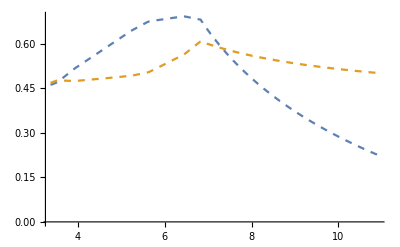

```mathematica
astraplot=ListLinePlot[{Transpose[{z,xrms}],Transpose[{z,yrms}]},PlotRange->All,PlotStyle->Dashed]
```

```mathematica
gamma=1+(Ekin/0.511);
```

```mathematica
ϵx=10^-6 ϵxnorm/gamma;
```

```mathematica
ϵy=10^-6 ϵynorm/gamma;
```

```mathematica
sddsInterpret["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\CLA.twi",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {s, betax, alphax, psix, etax, etaxp, xAperture, betay, alphay, psiy, etay, etayp, yAperture, pCentral0, ElementName, ElementOccurence, ElementType, dI1, dI2, dI3, dI4, dI5}

Parameters (Re)Assigned: {Step, nux, dnuxdp, dnuxdp2, dnuxdp3, Ax, nuy, dnuydp, dnuydp2, dnuydp3, Ay, deltaHalfRange, nuxChromUpper, nuxChromLower, nuyChromUpper, nuyChromLower, Stage, pCentral, dbetaxdp, dbetaydp, dalphaxdp, dalphaydp, etax2, etay2, etax3, etay3, etaxp2, etayp2, etaxp3, etayp3, betaxMin, betaxAve, betaxMax, betayMin, betayAve, betayMax, etaxMax, etayMax, waistsx, waistsy, dnuxdAx, dnuxdAy, dnuydAx, dnuydAy, dnuxdAx2, dnuxdAy2, dnuxdAxAy, dnuydAx2, dnuydAy2, dnuydAxAy, nuxTswaLower, nuxTswaUpper, nuyTswaLower, nuyTswaUpper, couplingIntegral, couplingDelta, emittanceRatio, alphac2, alphac, I1, I2, I3, I4, I5, ex0, enx0, taux, Jx, tauy, Jy, Sdelta0, taudelta, Jdelta, U0}

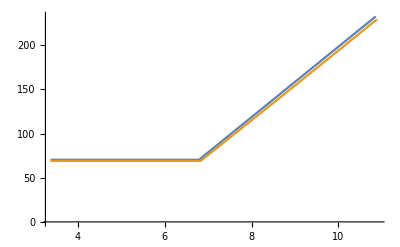

```mathematica
ListLinePlot[{Transpose[{s+z[[1]],pCentral0}],Transpose[{z,gamma}]},PlotRange->All]
```

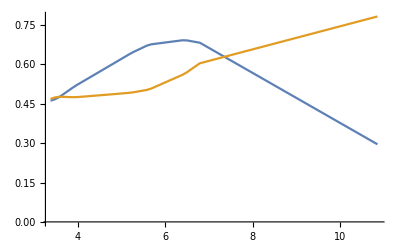

```mathematica
eleplot=ListLinePlot[{Transpose[{s+z[[1]],10^3 √(betax ϵx[[1]])}],Transpose[{s+z[[1]],10^3 √(betay ϵy[[1]])}]},PlotRange->All]
```

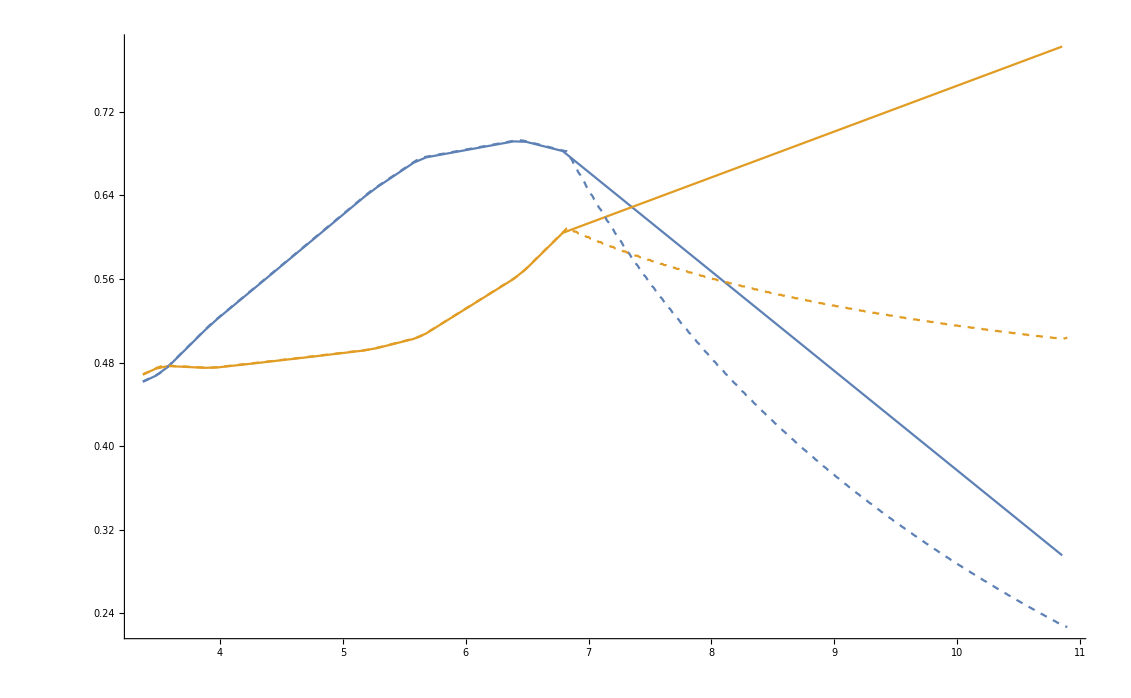

```mathematica
Show[eleplot,astraplot,PlotRange->All]
```